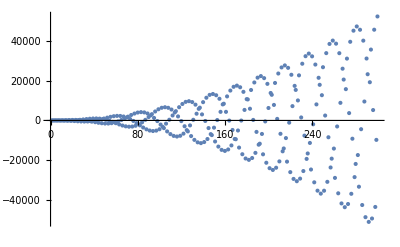

```mathematica
a=ListPlot[Table[Re[Sum[E^{-I (2 n+4)}(n+1)(n+2),{n,k}]][[1]]//N,{k,1,300}]]
```

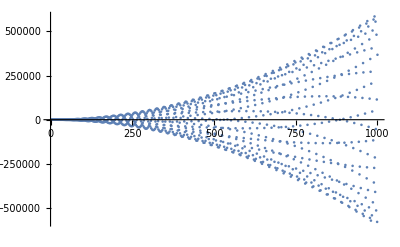

```mathematica
a = ListPlot[Table[Re[Sum[E^{-I (2 n+4)}(n+1)(n+2),{n,k}]][[1]]//N,{k,1,1000}]]
```

```mathematica
Manipulate[Show[{a,Plot[x^2/1.67*Sin[x/10.542],{x,0,1000},PlotStyle->Opacity[.5]],Plot[x^2/1.67*Sin[x/10.542+offset],{x,0,1000},PlotStyle->Opacity[.5]],Plot[x^2/1.67*Sin[x/10.542+4.28],{x,0,1000},PlotStyle->Opacity[.5]]}],{offset,0,10}]
```

Show::gcomb: Could not combine the graphics objects in Show[{a,,,}].